### Scratch notes and plots for ps8 (e)

```mathematica
<<peeters` ;
peeters`setGitDir[ "blogit" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

```mathematica
ContourPlot3D[ 1/Abs[ Sin[u] + Sin[v]] == e, {u, -Pi, Pi}, {v, -Pi, Pi}, {e, 0, 10}]
```

-Graphics3D-

```mathematica
Simplify[ Sin[ArcCos[a]]]
```

√(1-a^2)

```mathematica
$Assumptions = a > 0 ;
Clear[i]
i = Integrate[ E^(-2a Sqrt[x^2 + y^2 + z^2]) x^2, {x, -Infinity, Infinity}, {y, -Infinity, Infinity}, {z, -Infinity, Infinity}]
```

∫_(-∞)^∞ ∫_(-∞)^∞ ∫_(-∞)^∞ ⅇ^(-2 a √(x^2+y^2+z^2)) x^2ⅆzⅆyⅆx

```mathematica
i =  Integrate[ E^(-2a r) r^4 Sin[theta]^3 Cos[phi]^2, {r, 0, Infinity}, {theta, 0, Pi}, {phi, 0, 2 Pi}]
```

π/a^5

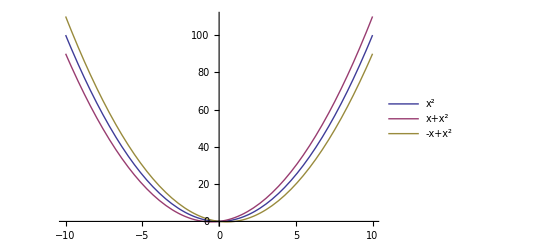

```mathematica
Plot[Evaluate@{x^2, x^2 + x, x^2 - x}, {x, -10, 10}, PlotLegends->"Expressions"]
```

```mathematica
Manipulate[
ContourPlot3D[ Cos[u] + Cos[v]== -mu  E^n, {u, -Pi, Pi}, {v, -Pi, Pi}, {mu, -2, 2}],
{n, 1/2, 5, 1/2}
]
```

```mathematica
Manipulate[
DynamicModule[{t, ticks},
t = Cos[u] + by Cos[v] == 2 #Sqrt[by^2 + 1] &/@ Table[n, {n, -1, 1, 0.1}] ;
ticks = Table[n, {n, -Pi, Pi, Pi/2}] ;
ContourPlot[ 
Evaluate@t
, {u, -Pi, Pi}
, {v, -Pi, Pi}
, FrameTicks -> {ticks, ticks}
, FrameLabel->{"k_x a", "k_y a"}
]
]
,{{by, 0.406}, 0, 1}
]
```

```mathematica
Clear[p]
p =DynamicModule[{by=0.406},DynamicModule[{t,ticks},t=(Cos[u]+by Cos[v]==2 #1 √(by^2+1)&)/@Table[n,{n,-1,1,0.1}];ticks=Table[n,{n,-π,π,π/2}];ContourPlot[Evaluate[t],{u,-π,π},{v,-π,π},FrameTicks->{ticks,ticks},FrameLabel->{"\!\(\*SubscriptBox[\(k\), \(x\)]\) a","\!\(\*SubscriptBox[\(k\), \(y\)]\) a"}]]]
```

```mathematica
peeters`exportForLatex["qmSolidsPs8eFig2", p]
```

{C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs8eFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit/qmSolidsPs8eFig2pn.png}